Рассмотрим интегралы I1 и I2:

```mathematica
I1=Integrate[(1-((1-Sqrt[1-ϵ^2/x^2])/(1+Sqrt[1-ϵ^2/x^2]))^2)*x,{x,ϵ,1}]
```

ConditionalExpression[(2 (-2+3 ϵ^2-ϵ^6+2 √(1-ϵ^2)-2 ϵ^2 √(1-ϵ^2)))/(3 ϵ^4),((Re[ϵ/(1-ϵ)]≥0&&ϵ≠0)||ϵ/(1-ϵ)∉Reals||Re[ϵ/(1-ϵ)]<-1)&&(Re[ϵ]>1||(ϵ∉Reals&&(Re[ϵ]≥0||Re[(ϵ^2 (Im[ϵ]^2+(-1+Re[ϵ]) Re[ϵ])^2)/((Im[ϵ]^2+Re[ϵ] (-ϵ+Re[ϵ]))^2)]≤1))||0<Re[ϵ]<1)]

```mathematica
I1=Expand[Simplify[I1,Assumptions->{0<ϵ<1}]]
```

-4/(3 ϵ^4)+2/ϵ^2-(2 ϵ^2)/3+(4 √(1-ϵ^2))/(3 ϵ^4)-(4 √(1-ϵ^2))/(3 ϵ^2)

В матлабовском коде встречается следующее выражение для того же интеграла:

```mathematica
I1m = 1/2 *(ϵ^2 + 1/ϵ^2) - 1 + (1/4)*(1-2/ϵ^2)*Sqrt[1-ϵ^2]-(ϵ^2/8)*Log[ϵ^2/(2-ϵ^2+2*Sqrt[1-ϵ^2])]
```

-1+1/4 (1-2/ϵ^2) √(1-ϵ^2)+1/2 (1/ϵ^2+ϵ^2)-1/8 ϵ^2 Log[ϵ^2/(2-ϵ^2+2 √(1-ϵ^2))]

На графике видно, что кто-то очень неправ

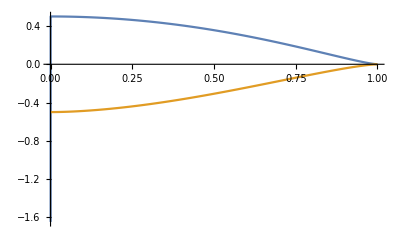

```mathematica
Plot[{I1, I1m},{ϵ,0,1}]
```

Теперь второй интеграл

```mathematica
I2=Integrate[(1-((1-Sqrt[1-ϵ^2/x^2])/(1+Sqrt[1-ϵ^2/x^2]))^2)*x^2,{x,ϵ,1}]
```

ConditionalExpression[(4 (-30+42 ϵ^2-12 ϵ^7+30 √(1-ϵ^2)-27 ϵ^2 √(1-ϵ^2)-ϵ^4 √(1-ϵ^2)-2 ϵ^6 √(1-ϵ^2)))/(105 ϵ^4),((Re[ϵ/(1-ϵ)]≥0&&ϵ≠0)||ϵ/(1-ϵ)∉Reals||Re[ϵ/(1-ϵ)]<-1)&&(Re[ϵ]>1||(ϵ∉Reals&&(Re[ϵ]≥0||Re[(ϵ^2 (Im[ϵ]^2+(-1+Re[ϵ]) Re[ϵ])^2)/((Im[ϵ]^2+Re[ϵ] (-ϵ+Re[ϵ]))^2)]≤1))||0<Re[ϵ]<1)]

```mathematica
I2=Expand[Simplify[I2,Assumptions->{0<ϵ<1}]]
```

-8/(7 ϵ^4)+8/(5 ϵ^2)-(16 ϵ^3)/35-(4 √(1-ϵ^2))/105+(8 √(1-ϵ^2))/(7 ϵ^4)-(36 √(1-ϵ^2))/(35 ϵ^2)-8/105 ϵ^2 √(1-ϵ^2)

```mathematica
I2m = (2/3)*(1-ϵ^3)+(2/3)*(1-ϵ^2)^(3/2)-(2/(5*ϵ^2))*(1-ϵ^5)+(2/(5*ϵ^2))*(1-ϵ^2)^(5/2)
```

2/3 (1-ϵ^2)^(3/2)+(2 (1-ϵ^2)^(5/2))/(5 ϵ^2)+2/3 (1-ϵ^3)-(2 (1-ϵ^5))/(5 ϵ^2)

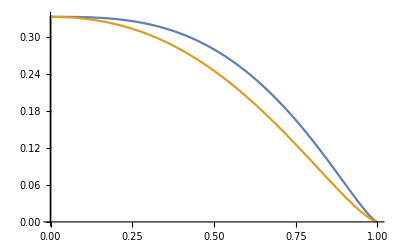

```mathematica
Plot[{I2,I2m},{ϵ,0,1}]
```

Здесь уже больше похоже на правду

Теперь займёмся решением задачи. Для этого нам нужны следующие величины:

511003.

2.81794×10^-13

6.02214×10^23

0.00729735

5.35

32

72.6

12.5

(0.000171324 (1.13+(0.20503 (1+T)^2)/(T (2+T))))/(T (2+T))

0.000670752

(1.41707 (1+T)^2 Log[1738.35 T])/(T (2+T))

(0.0427686 T^2 (2+T)^2)/((1+T)^2 (-1/(1+(0.000171324 (1.13+(0.20503 (1+T)^2)/(T (2+T))))/(T (2+T)))+Log[1+(5836.9 T (2+T))/(1.13+(0.20503 (1+T)^2)/(T (2+T)))]))

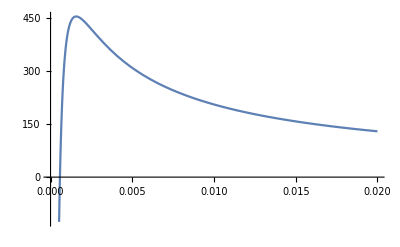

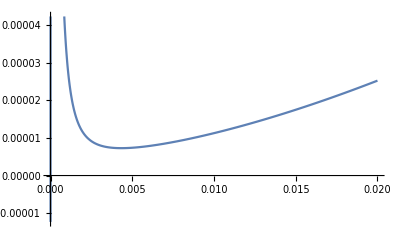

0.08 T

-32552.1/T^4+312.5/T^2-0.00426667 T^2+(32552.1 √(1-0.0064 T^2))/T^4-(208.333 √(1-0.0064 T^2))/T^2

-27901.8/T^4+250./T^2-0.000234057 T^3-4/105 √(1-0.0064 T^2)+(27901.8 √(1-0.0064 T^2))/T^4-(160.714 √(1-0.0064 T^2))/T^2-0.000487619 T^2 √(1-0.0064 T^2)

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

NDSolve::ndinpd: The initial conditions did not evaluate to an array of numbers of depth 1 on the spatial grid. Initial conditions for partial differential equations should be specified as scalar functions of the spatial variables.

NDSolve[{u^(1,0)[T,x]==(0.0100603 T^3 (2+T)^3 u^(0,2)[T,x])/((1+T)^4 Log[1738.35 T] (-1/(1+(0.000171324 (1.13+(0.20503 (1+T)^2)/(T (2+T))))/(T (2+T)))+Log[1+(5836.9 T (2+T))/(1.13+(0.20503 (1+T)^2)/(T (2+T)))])),u[0.02,x]==Sin[πx],u[T,1]==0,u[T,0]==0},u,{T,0.02,0.05},{x,0,1}]

NDSolve::dsvar: 0.0200021 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0200021 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.022145 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics3D-

```mathematica
Subscript[E, e] = 511003.4
Subscript[r, e]=2.8179403267*10^-13
Subscript[N, a] =6.0221413*10^23
α = 0.00729735256
ρ= 5.3500
Z = 32
M=72.600
Subscript[U, 0]=12.5
η=1/4((α Z^(1/3))/0.885)^2 1/(T(T+2))(1.13+3.76α^2Z^2(T+1)^2/(T(T+2)))
J = Piecewise[{{13.6Z / Subscript[E, e],Z < 10},{(9.76 + 58.8Z^-1.19)Z / Subscript[E, e],Z ≥ 10}}]
ϵ =  (2 π ρ Subscript[N, a] Z)/M ((T+1)^2 Subscript[r, e]^2)/(T(T+2))(2Log[1.166T/J])
Subscript[λ, tr]=((2 π ρ Subscript[N, a] Z(Z+1))/M ((T+1)^2 Subscript[r, e]^2)/(T^2(T+2)^2)(Log[1+1/η]-1/(η+1)))^-1
Plot[ϵ,{T, 0, 0.02}]
Plot[Subscript[λ, tr],{T, 0, 0.02}]
t = T/Subscript[U, 0]
Subscript[I, 1]=-4/(3 t^4)+2/t^2-(2 t^2)/3+(4 √(1-t^2))/(3 t^4)-(4 √(1-t^2))/(3 t^2)
Subscript[I, 2]=-8/(7 t^4)+8/(5 t^2)-(16 t^3)/35-(4 √(1-t^2))/105+(8 √(1-t^2))/(7 t^4)-(36 √(1-t^2))/(35 t^2)-8/105 t^2 √(1-t^2)
```